```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v3/phase/phase_boundary

```mathematica
mf=Table[Transpose[Import["./TemB"<>ToString[i]<>"/BUFFER/MF.DAT"]][[1]],{i,1,40}];
intdmfdt=Table[-D[Interpolation[mf[[i]]][x],x],{i,1,40}];
mub=Table[i*15,{i,1,38}];
Tpc=Table[FindMaximum[{intdmfdt[[i]],90<x<170},{x,140}][[2]][[1]][[2]],{i,1,38}];
peak=Table[FindMaximum[{intdmfdt[[i]],90<x<170},{x,140}][[1]],{i,1,38}];
Tpcup80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]+2}][[1]][[2]],{i,1,38}];
Tpcdown80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]-2}][[1]][[2]],{i,1,38}];
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

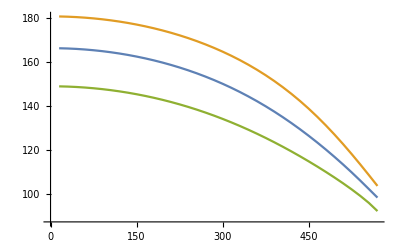

```mathematica
ListLinePlot[{Transpose[{mub,Tpc}],Transpose[{mub,Tpcup80}],Transpose[{mub,Tpcdown80}]}]
```

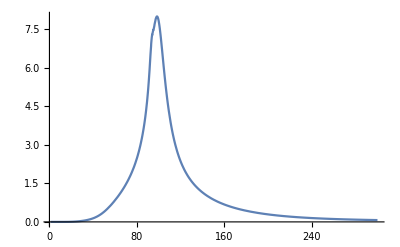

```mathematica
Plot[intdmfdt[[38]],{x,1,300},PlotRange->All]
```